DVOJITÁ GEOMETRICKÁ TRANSFORMÁCIA PRIAMKY

==========================================

POČIATOČNÁ PRIAMKA:

Body priamky AB:

(-7 | -7
-2 | -3)

Vlastnosti priamky:

Dĺžka úsečky: √41

Rovnica priamky: y = 4/5x - 7/5

Priesečník s osou x: [7/4, 0]

Priesečník s osou y: [0, -7/5]

PRVÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE PRIAMKY - POSUN

========================================

ZADANIE:

Majme priamku AB s bodmi:

(-7 | -7
-2 | -3)

Vykonajte posun priamky v 2D priestore pomocou vektora posunu: Δ = [-4, 3]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -4
0 | 1 | 3
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -4

dy = 3

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre jednotlivé body:

Bod A:

Pôvodné súradnice: [-7, -7]

Výpočet x-ovej súradnice:

x' = x + dx = -7 + -4

x' = -11

Výpočet y-ovej súradnice:

y' = y + dy = -7 + 3

y' = -4

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -11 + (4) = -7

y = y' + (-dy) = -4 + (-3) = -7

Maticový zápis:

(1 | 0 | -4
0 | 1 | 3
0 | 0 | 1) · (-7
-7
1) = (-11
-4
1)

Bod B:

Pôvodné súradnice: [-2, -3]

Výpočet x-ovej súradnice:

x' = x + dx = -2 + -4

x' = -6

Výpočet y-ovej súradnice:

y' = y + dy = -3 + 3

y' = 0

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -6 + (4) = -2

y = y' + (-dy) = 0 + (-3) = -3

Maticový zápis:

(1 | 0 | -4
0 | 1 | 3
0 | 0 | 1) · (-2
-3
1) = (-6
0
1)

VÝSLEDOK:

Body priamky po posune:

(-11 | -4
-6 | 0)

VIZUALIZÁCIA:

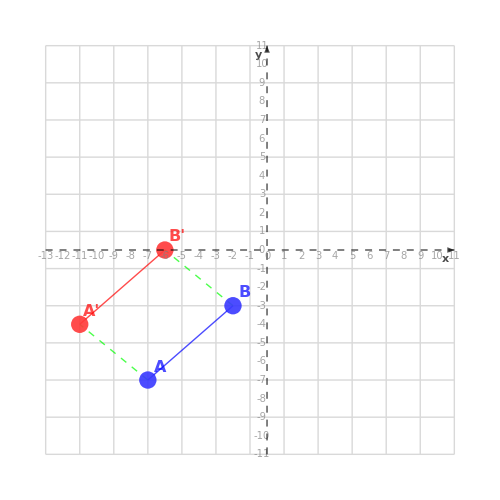

LEGENDA:

• Modré body a čiary: Pôvodná priamka

• Červené body a čiary: Posunutá priamka

• Zelená šípka: Vektor posunu

• Zelené prerušované čiary: Posun jednotlivých bodov

• Mriežka: Súradnicový systém

Pôvodné body (modrá):

Bod A: {-7,-7}

Bod B: {-2,-3}

Výsledné body (červená):

Bod A': {-11,-4}

Bod B': {-6,0}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [4, -3] (opačný vektor)

DRUHÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE PRIAMKY - ROTÁCIA

========================================

ZADANIE:

Majme priamku AB s koncovými bodmi:

(-11 | -4
-6 | 0)

Vykonajte rotáciu priamky v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 60°.

Transformačná matica rotácie:

(1/2 | -(√3)/2
(√3)/2 | 1/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnotu α = 60°:

cos(α) = 1/2

sin(α) = √3/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre jednotlivé body:

Bod A:

Pôvodné súradnice: [-11, -4]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -11 · 1/2 - -4 · √3/2

x' = -11/2 + 2 · √3

x' = -11/2 + 2 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -11 · √3/2 + -4 · 1/2

y' = -2 - (11 · √3)/2

y' = -2 - (11 · √3)/2

Výsledné súradnice: [-11/2 + 2 · √3, -2 - (11 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = -11/2 + 2 · √3 · 1/2 - -2 - (11 · √3)/2 · -1/2 · √3

x = -11

x = -11 = -11

y = x' · sin(α') + y' · cos(α')

y = -11/2 + 2 · √3 · -1/2 · √3 + -2 - (11 · √3)/2 · 1/2

y = -4

y = -4 = -4

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (-11
-4) = (-11/2+2 √3
-2-(11 √3)/2)

Bod B:

Pôvodné súradnice: [-6, 0]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -6 · 1/2 - 0 · √3/2

x' = -3

x' = -3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -6 · √3/2 + 0 · 1/2

y' = -3 · √3

y' = -3 · √3

Výsledné súradnice: [-3, -3 · √3]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = -3 · 1/2 - -3 · √3 · -1/2 · √3

x = -6

x = -6 = -6

y = x' · sin(α') + y' · cos(α')

y = -3 · -1/2 · √3 + -3 · √3 · 1/2

y = 0

y = 0 = 0

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (-6
0) = (-3
-3 √3)

VÝSLEDOK:

Body priamky po rotácii:

(-11/2+2 √3 | -2-(11 √3)/2
-3 | -3 √3)

VIZUALIZÁCIA:

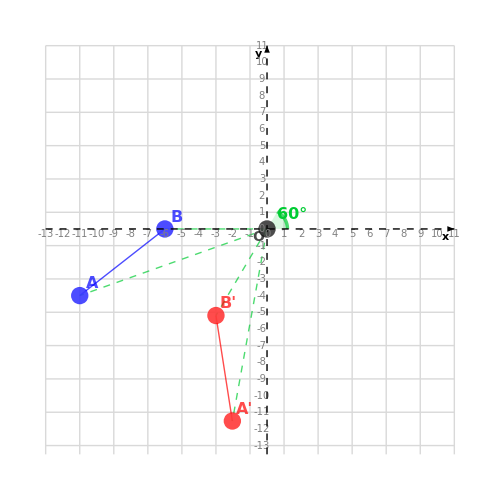

LEGENDA:

• Modré body a čiary: Pôvodná priamka

• Červené body a čiary: Otočená priamka

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia bodov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné body (modrá):

Bod A: {-11,-4}

Bod B: {-6,0}

Výsledné body (červená):

Bod A': {-11/2+2 √3,-2-(11 √3)/2}

Bod B': {-3,-3 √3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -60°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť všetkých bodov od počiatku sústavy [0,0]

• Rotácia nemení veľkosť ani tvar geometrických útvarov - je to izometria

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

TABUĽKA ŠPECIÁLNYCH HODNÔT:

Hodnoty pre najčastejšie uhly:

α | sin(α) | cos(α)
0° | 0 | 1
30° | 1/2 | √3/2
45° | 1/√2 | 1/√2
60° | √3/2 | 1/2
90° | 1 | 0
120° | √3/2 | -1/2
135° | 1/√2 | -1/√2
150° | 1/2 | -√3/2
180° | 0 | -1
270° | -1 | 0
360° | 0 | 1

SÚHRN TRANSFORMÁCIÍ:

Pôvodná priamka AB: (-7 | -7
-2 | -3)

Po prvej transformácii (Posun): (-11 | -4
-6 | 0)

Po druhej transformácii (Rotácia): (-11/2+2 √3 | -2-(11 √3)/2
-3 | -3 √3)

SÚHRNNÁ VIZUALIZÁCIA:

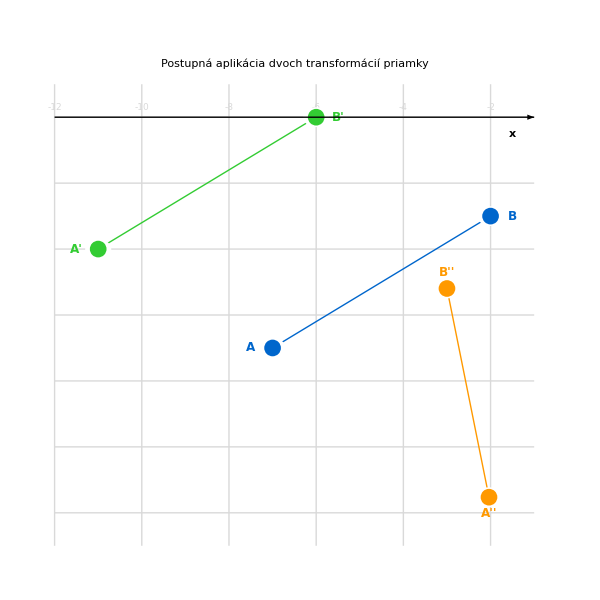

LEGENDA:

• Modré body a čiary: Pôvodná priamka AB

• Zelené body a čiary: Priamka A'B' po prvej transformácii (Posun)

• Oranžové body a čiary: Priamka A''B'' po druhej transformácii (Rotácia)

{{{-7,-7},{-2,-3}},{{-11,-4},{-6,0}},{{-11/2+2 √3,-2-(11 √3)/2},{-3,-3 √3}},Posun,Rotácia}

```mathematica
PriamkaDvojitaTransformacia[]
```